# StudentT

```mathematica
dist=StudentTDistribution[n]
```

StudentTDistribution[n]

```mathematica
PDF[dist,z]
```

((n/(n+z^2))^((1+n)/2))/(√n Beta[n/2,1/2])

```mathematica
CDF[dist,z]
```

Piecewise[{{1/2 BetaRegularized[n/(n+z^2),n/2,1/2], z≤0}, {1/2 (1+BetaRegularized[z^2/(n+z^2),1/2,n/2]), True}}]

```mathematica
Manipulate[Plot[PDF[StudentTDistribution[n],x],{x,-5,5},Filling->Axis],{n,0.1,4}]
```

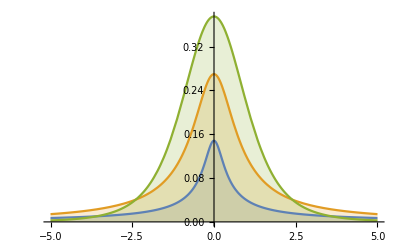

```mathematica
Plot[Table[PDF[StudentTDistribution[ν],x],{ν,{0.1,0.5,4}}]//Evaluate,{x,-5,5},Filling->Axis]
```

```mathematica
Mean[dist]
```

Piecewise[{{0, n>1}, {Indeterminate, True}}]

```mathematica
Median[dist]
```

0

```mathematica
Variance[dist]
```

Piecewise[{{n/(-2+n), n>2}, {Indeterminate, True}}]

```mathematica
StandardDeviation[dist]
```

Piecewise[{{√(n/(-2+n)), n>2}, {Indeterminate, True}}]

```mathematica
Skewness[dist]
```

Piecewise[{{0, n>3}, {Indeterminate, True}}]

```mathematica
Kurtosis[dist]
```

Piecewise[{{3+6/(-4+n), n>4}, {Indeterminate, True}}]

```mathematica
CharacteristicFunction[dist,t]
```

(2^(1-n/2) n^(n/4) Abs[t]^(n/2) BesselK[n/2,√n Abs[t]])/Gamma[n/2]

```mathematica
Random[StudentTDistribution[1]]
```

0.39277